```mathematica
Import["C:\Users\DFCTech\Downloads\SAT_data\cs159\SATALL12S_data\SATALL12Sft_and_slv_times_with_vals.csv"]
```

{{INSTANCE_ID,ebglucose_Time,ebminisat_Time,glucose2_Time,glueminisat_Time,lingeling_Time,lrglshr_Time,144,gsat_FirstLocalMinRatio_Mean,gsat_FirstLocalMinRatio_CoeffVariance,ls_gsat_featuretime,lobjois_mean_depth_over_vars,lobjois_log_num_nodes_over_vars,lobjois_featuretime},1613,{1}}
 |  |  |  |

```mathematica
d=%;
```

```mathematica
d⟦1,2;;32⟧//Length
```

31

```mathematica
Position[Map[StringContainsQ["featuretime"],d⟦1⟧],True]-2
```

{{37},{52},{73},{84},{90},{109},{128},{140},{152},{155}}

```mathematica
Position[Map[StringContainsQ[#,"featuretime"] || StringContainsQ[#,"Time"]&,d⟦1⟧],False]-2
```

{{-1},{31},{32},{33},{34},{35},{36},{38},{39},{40},{41},{42},{43},{44},{45},{46},{47},{48},{49},{50},{51},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{63},{64},{65},{66},{67},{68},{69},{70},{71},{72},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{85},{86},{87},{88},{89},{91},{92},{93},{94},{95},{96},{97},{98},{99},{100},{101},{102},{103},{104},{105},{106},{107},{108},{110},{111},{112},{113},{114},{115},{116},{117},{118},{119},{120},{121},{122},{123},{124},{125},{126},{127},{129},{130},{131},{132},{133},{134},{135},{136},{137},{138},{139},{141},{142},{143},{144},{145},{146},{147},{148},{149},{150},{151},{153},{154}}

```mathematica
d⟦1,39⟧
```

Pre_featuretime

```mathematica
d⟦1⟧⟦20⟧
```

mphaseSATm_Time

```mathematica
Transpose[d]⟦20⟧//Mean/.{"mphaseSATm_Time"->0}
```

```mathematica
(662134.6000000001+0)/1615
```

409.99

```mathematica
Graph[1]
```

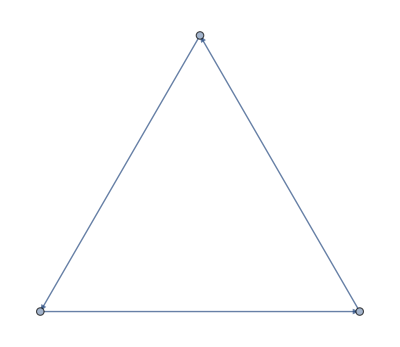

```mathematica
Graph[{1->2,2->3,3->1},EdgeShapeFunction->GraphElementData[{"HalfFilledArrow","ArrowSize"->.1}]]
```

```mathematica
Export["C:\\Users\\DFCTech\\Desktop\\figures\\d.svg",Graph[Join[Table[1->i,{i,2,4}],Table[3->i,{i,5,9}]],ImageSize->Large]]
```

C:\Users\DFCTech\Desktop\figures\d.svg

{1->2,1->3,1->4,2->5,2->6,2->7,2->8,2->9,2->10}

```mathematica
d1=Import["C:\\Users\\DFCTech\\Downloads\\SATALL12S_for_ajay (1).csv"];
```

```mathematica
d2=d1⟦2;;⟧⟦All;;-1⟧
```

{1}
 |  |  |  |

```mathematica
d2=d1⟦2;;⟧
```

{1}
 |  |  |  |

```mathematica
deugene=Transpose[d2]⟦-1⟧;
```

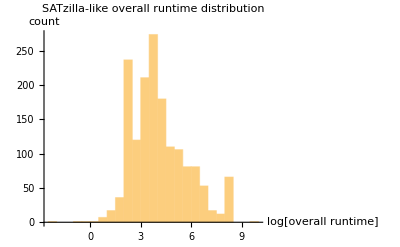

```mathematica
heugene=Histogram[Log[deugene],PlotRange->{All,Automatic},AxesLabel->{"log[overall runtime]","count"},PlotLabel->"SATzilla-like overall runtime distribution"]
```

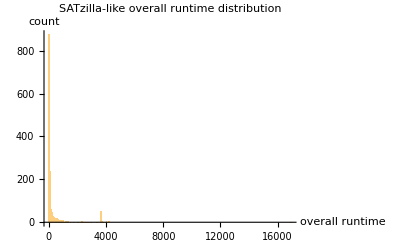

```mathematica
heugenenorm=Histogram[deugene,PlotRange->{All,Automatic},AxesLabel->{"overall runtime","count"},PlotLabel->"SATzilla-like overall runtime distribution"]
```

```mathematica
dddqn=Import["C:\\Users\\DFCTech\\ddqn1.csv"]⟦All,1⟧;
```

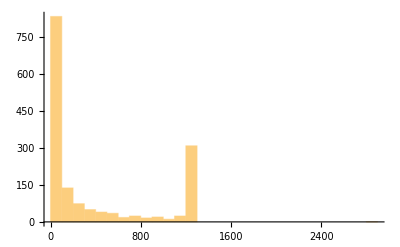

```mathematica
hddqn=Histogram[Sort[dddqn]⟦21;;-1⟧]
```

```mathematica
Mean[]
```

376.297848180677541

```mathematica
ouralgo=Import["C:\\Users\\DFCTech\\ouralgo.csv"]⟦All,1⟧;
```

```mathematica
Mean[Sort[ouralgo]⟦19;;-1⟧]
```

317.761560150375938

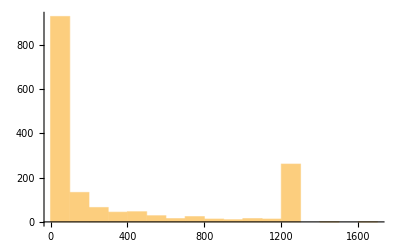

```mathematica
houralgo=Histogram[Sort[ouralgo]⟦19;;-1⟧]
```

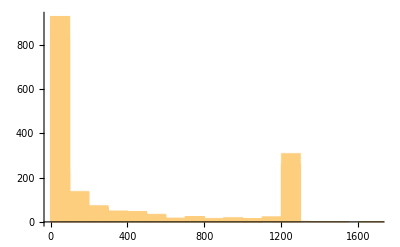

```mathematica
Show[houralgo,heugene,hddqn]
```

```mathematica
switch=Import["C:\\Users\\DFCTech\\switchdec.csv"];
```

```mathematica
vs=Map[Round,switch]⟦All,1⟧;
```

```mathematica
v = Association[{3->Red,16->Blue,18->Orange}];
```

```mathematica
as=GroupBy[Transpose[{Range[Length[vs]],vs}],Last];
```

```mathematica
points=Map[Transpose[{#⟦All,1⟧,Range[Length[#]]}]&,Values[as]];
```

```mathematica
vs//Length
```

13201

```mathematica
Flatten[points]//Max
```

13201

{sparrow,mphaseSAT,glueminisat,mphaseSATm,sol}

{RGBColor[0.24531153120011062, 0.6896901031609171, 0.015191485398532878],RGBColor[0.9589544934477756, 0.3486782935597519, 0.7655452730789007],RGBColor[0.37765370334079007, 0.08723906246574487, 0.490036484306976],RGBColor[0.30842295402571085, 0.9428494366406086, 0.7426351823184882],RGBColor[0.7925105757600117, 0.8685709078904125, 0.05204815389875339]}

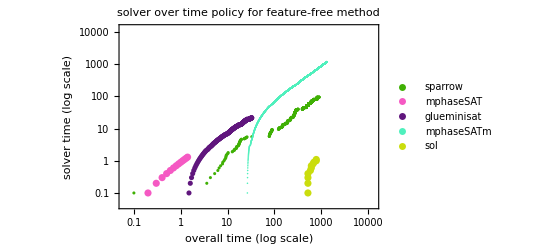

```mathematica
labels=Map[StringTake[#,1;;-6]&,d⟦1,Keys[as]+2⟧]
colors = Table[RandomColor[],Length[labels]]
result=Show[MapThread[ListLogLogPlot[Transpose[{#1⟦All,1⟧/10,#1⟦All,2⟧/10}],PlotStyle->#3,PlotRange->{{0,Length[vs]},{0,Length[vs]}},Filling->None,PlotLegends->LineLegend[{#3},{#2}]]&,{points,labels,colors}],Axes->False,Frame->{{True,False},{True,False}},FrameLabel->{{"solver time (log scale)",None},{"overall time (log scale)",None}},PlotLabel->"solver over time policy for feature-free method"]
```

```mathematica
Export["featureless.svg",result]
```

featureless.svg

```mathematica
Map[StringTake[#,1;;-6]&,d⟦1,Keys[as]+2⟧]
```

{sparrow,mphaseSAT,glueminisat,mphaseSATm,sol}

```mathematica
switchts=Import["C:\\Users\\DFCTech\\switchtimes.csv",""]⟦All,1⟧;
```

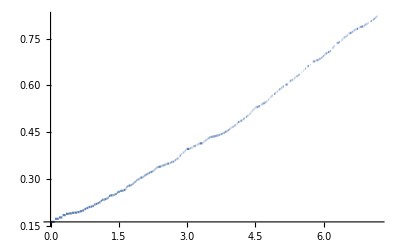

```mathematica
Plot[CDF[EmpiricalDistribution[Log[switchts+0.1]],x],{x,0,Log[Max[switchts]]}]
```

```mathematica
rts=Import["C:\\Users\\DFCTech\\rts.csv","Table"]⟦All,1⟧;
```

```mathematica
rts//Length
```

1614

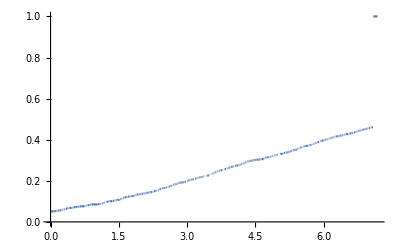

```mathematica
Plot[CDF[EmpiricalDistribution[Log[rts+0.1]],x],{x,0,Log[Max[switchts]]}]
```